```mathematica
Guy F. Mongelli;
Prof. J. Admin Mann;
ECHE 475;
9/19/2012;
```

```mathematica
Clear[x,y,z,r,θ,ϕ]
```

```mathematica
Problem 1:
```

```mathematica
The domain will specify which values r, θ and ϕ can take.  r is the set of all real numbers.  θ is the set of all real numbers but is typically translated until it is within the value from zero to 2π.  ϕ, the aximithul or inclinational angle may realistically take all real numbers but for simplification is restricted from zero to π.  The codomain will specify the values that x,y and z may take.  x, y, and z may all be represented by all real numbers.
```

```mathematica
As a practice assesment, I will evaluate the 2D case:
```

```mathematica
x=r*Cos[θ]
y=r*Sin[θ]
```

r Cos[θ]

r Sin[θ]

```mathematica
df=MatrixForm[({{D[x,r], D[x,θ]}, {D[y,r], D[y,θ]}})]
```

(Cos[θ] | -r Sin[θ]
Sin[θ] | r Cos[θ])

```mathematica
Det[%]//Simplify
```

r

```mathematica
Clear[x,y,z,r,θ,ϕ]
```

```mathematica
Since the determinant is non-zero, this matrix does contains a set of linearly independent vectors.
```

```mathematica
let x,y, and z be defined as follows:
```

```mathematica
x=r*Sin[θ]*Cos[ϕ]
y=r*Sin[θ]Sin[ϕ]
z=r*Cos[θ]
```

r Cos[ϕ] Sin[θ]

r Sin[θ] Sin[ϕ]

r Cos[θ]

```mathematica
let the vector f be defined as;
```

```mathematica
f=MatrixForm[({{x}, {y}, {z}})]
```

(r Cos[ϕ] Sin[θ]
r Sin[θ] Sin[ϕ]
r Cos[θ])

```mathematica
df=MatrixForm[({{D[x,r], D[x,θ], D[x,ϕ]}, {D[y,r], D[y,θ], D[y,ϕ]}, {D[z,r], D[z,θ], D[z,ϕ]}})]
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
Det[({{D[x,r], D[x,θ], D[x,ϕ]}, {D[y,r], D[y,θ], D[y,ϕ]}, {D[z,r], D[z,θ], D[z,ϕ]}})]
```

r^2 Cos[θ]^2 Cos[ϕ]^2 Sin[θ]+r^2 Cos[ϕ]^2 Sin[θ]^3+r^2 Cos[θ]^2 Sin[θ] Sin[ϕ]^2+r^2 Sin[θ]^3 Sin[ϕ]^2

```mathematica
FullSimplify[Det[({{D[x,r], D[x,θ], D[x,ϕ]}, {D[y,r], D[y,θ], D[y,ϕ]}, {D[z,r], D[z,θ], D[z,ϕ]}})]]
```

r^2 Sin[θ]

```mathematica
There is an implied dr dθ dϕ in the line above, such that dx dy=r^2 Sin[θ]dr dθ dϕ.
```

```mathematica
Clear[x,y,z,r,θ,ϕ]
```

```mathematica
We can force Mathematica to give us the Jacobian matrix and it's determinanat of any corrdinate system that we should like.  Even relative to other coordinate system transofrmations.  This mapping may be characterized as onto and one-to-one.
```

```mathematica
Needs["VectorAnalysis`"];
```

```mathematica
JacobianMatrix[{r, θ, ϕ}, Spherical]//MatrixForm
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
Det[%]//Simplify
```

r^2 Sin[θ]

```mathematica
JacobianDeterminant[{r, θ,ϕ}, Spherical]
```

r^2 Sin[θ]

```mathematica
The matrix associated with coordinate transformation from spherical to carthesian contains vectors that are linearly independent as evidenced by a non-zero determinant (Jacobian).
```

```mathematica
For the other coordinate system transformations of interest:
```

```mathematica
JacobianMatrix[{x, y, z},Cartesian]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
JacobianDeterminant[{x, y, z},Cartesian]
```

1

```mathematica
Clear[x,y,z]
```

```mathematica
Problem 2:
```

```mathematica
The plot of the function is performed below.
```

```mathematica
Manipulate[Plot[D[Sin[x]/x,l],{x,-10,10},AxesLabel->{"x","Sin[x]/x"}],{l,1,10}]
```

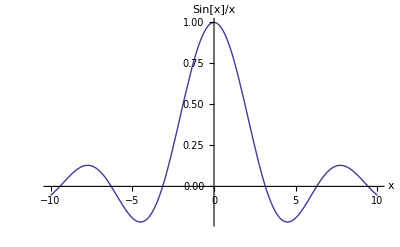

```mathematica
Plot[Sin[x]/x,{x,-10,10},AxesLabel->{"x","Sin[x]/x"}]
```

```mathematica
The first value returned in the next line is the global maximum of the function.  The second value is the corresponding x-value.  Note that the x-value is close enought to zero to be defined as just that.
```

```mathematica
FindMaximum[Sin[a]/a,a]
```

{1.,{a→5.13483×10^-10}}

```mathematica
The first value returned in the following line is the global minimum of the function.  The second value is the correspondinx x-value which is close enough to 4.49;
```

```mathematica
FindMinimum[Sin[a]/a,a]
```

{-0.217234,{a→4.49341}}

```mathematica
s[a_]=FullSimplify[D[Sin[a]/a,a]]
```

(a Cos[a]-Sin[a])/a^2

```mathematica
The global minimum and maximum specify the bounds on the codomain.  All real values may be taken within this set.  This can be represented as [-.217,1].  The domain is all reals except for 0, where the function is undefined. The function may be defnied by utilizing a peicewise function and then defining the value at x=0 as 1 (where the positive and negative limits of the function go to as x goes to zero).  Integration of this function across this value will require the improper integration technique,wherein the integral is split at the discontinuity and the function value at the duscontinuity will be defined as the positive or negative limit of the function value in the respective integral.;
```

```mathematica
Problem 3:
```

```mathematica
Performing the analysis of this question with the consideration of the information in Prof. Edward's notes-look at the logarithm of a complex number of the form z=a+bⅈ (Log []in Mathematica is the natural log):
```

```mathematica
From Prof. Edward's notes;
Log[a+b*ⅈ]=u=Log[|u|]+ⅈ(θ±k*2π)
```

```mathematica
where k can be any integer.
```

```mathematica
a and b are the domain and may take values of all real numbers.
```

```mathematica
In this case |u|=√((a+bⅈ)SuperStar[(a+bⅈ)])=√((a+bⅈ)(a-bⅈ))=√(a^2+b^2)
```

```mathematica
This square root, th e  norm, can only hold positive values since a and b are squared (the squared value of a real number is restricted to non-negative reals).  Therefore, 
|u| must be all non-negative real numbers.k  is an integer value that allows us to define θ ashaving values between [0,2π). This set is not inclusinve on one side since shifting the value of k may take 2π to zero.  Defining the bounds of u and θ specify the codomain.
```

```mathematica
Next, let us consider the complex exponentiation function.  In order to address the codomains of the logarithmic and exponential functions in the complex plane, we must first map x and y onto r and θ.
```

```mathematica
u=e^(a+ib)=r(Cos[θ]+ⅈ*Sin[θ]);
```

```mathematica
Using the following two relations:
```

```mathematica
u=|u|e^ⅈθ=r e^ⅈθ;
r=|u|=e^a=√(u SuperStar[u]);
```

```mathematica
where SuperStar[u] is the complex conjugate of u, as it was in the exponentiation function.
```

```mathematica
Re(u)=e^a Cos[y]
```

```mathematica
Im(u)=e^a Sin[y]
```

```mathematica
Since a and b may be the domain of all real numbers, r may be valued as all real numbers(including 0 only in the limit as a goes to negative infiniti). Negative values of the real part of the complex exponentiation function may be received from the cosine function.  The imaginary part of the complex exponentiation function can only be valued between ±1, and θ can be all real numbers.  In this definition of the exponentiation function, a shifting constant, k, has not been defined such taht θ is restricted to [0,2π).
```

```mathematica
This function is simmilar to converting from the complex plane into the real polar coordinate system.
```

```mathematica
Problem 4:
```

```mathematica
Clear[x,y,z]
```

```mathematica
Part A:The function is a density function because it implies how many particles are in a certain volumetric region.  So given a certain volume and particle spacing, a density is implied.  Equally, if a density is given and a total number of particles, a spacing may be determined and the same type of argument is true for density and total number of particles implies volume.
```

```mathematica
Part B:
```

```mathematica
Instead of x and Subscript[x, n],m and a will be used such that variables will not be duplicated in this notebook.  a will be written as a function, m[n], to be later defined.(Note: writting Subscript[m, n] in the cell produces an empty response in the Fourier transform function, but writing it m[n] works fine).
```

```mathematica
ρ[x_]=∑_(n=1)^N DiracDelta[x-x[n]]
```

∑_(n=1)^N DiracDelta[x-x[n]]

```mathematica
To show this is equivalent to the definition, the following is executed:
```

```mathematica
The next two cells give errors even when a is substituted for m[n].
```

```mathematica
∫_(-∞)^∞ Exp[-2Pi*ⅈ*x](∑_(n=1)^N DiracDelta[x-a])ⅆx
```

(1.+4.89859×10^-16 ⅈ) N

```mathematica
∫_(-∞)^∞ ⅇ^(-2 ⅈ π x) ∑_(n=1)^N DiracDelta[x-a]ⅆx
```

Integrate::nodiffd: ∫_-∞ ∞ ⅇ^-2 ⅈ π x ∑ n = 1 7 DiracDelta[x - a] ⅆ x cannot be interpreted. Integrals are entered in the form ∫fⅆx, where ⅆ is entered as EscddEsc.

```mathematica
However, the Fourier Transform function natively in Mathematica works.
```

```mathematica
Ρ[q_]=FourierTransform[ρ[m],m,q]
```

∑_(n=1)^N ⅇ^(ⅈ q m[n])/(√(2 π))

```mathematica
Define a row vector that contains the atomic positions:
```

a atomic contains Define positions row that the vector

```mathematica
To determine the norm, the complex conjugate of the fourier transformed  density functional is multiplied by it's non-conjugated form:
```

```mathematica
Conjugate[ⅈ]
```

-ⅈ

```mathematica
∑_(n=1)^N Conjugate[ⅇ^(I q m[n])/(√(2 π))]
```

∑_(n=1)^N ⅇ^(-ⅈ Conjugate[q m[n]])/(√(2 π))

```mathematica
Simplify[∑_(n=1)^N ⅇ^(-ⅈ q a)/(√(2 π))*(∑_(n=1)^N ⅇ^(ⅈ q a)/(√(2 π)))]
```

0.159155 N^2

```mathematica
N[1/(2*Pi)]
```

0.159155

```mathematica
This is for the one-dimensional case.
```

```mathematica
To create the 3D case, we first define:
```

```mathematica
m[n1_,n2_,n3_]=({{m1, m2, m3}})
```

{{m1,m2,m3}}

```mathematica
ρ3D[x_]=∑_(n=1)^N DiracDelta[x-m1-m2-m3]
```

N DiracDelta[m1+m2+m3-x]

```mathematica
Ρ3[q_]=FourierTransform[ρ3D[m],m,q]
```

(N (Cos[(m1+m2+m3) q]+ⅈ Sin[(m1+m2+m3) q]))/(√(2 π))

```mathematica
FullSimplify[((N (Cos[(m1+m2+m3) q]-ⅈ Sin[(m1+m2+m3) q]))/(√(2 π)))((N (Cos[(m1+m2+m3) q]+ⅈ Sin[(m1+m2+m3) q]))/(√(2 π)))]
```

N^2/(2 π)

```mathematica
Clear[a]
```

```mathematica
NewP[q_]=((1-Exp[-ⅈ*q a n])/(1-Exp[-ⅈ q a]));
```

```mathematica
Conjugate[((1-Exp[-I*q a n])/(1-Exp[-I q a]))]
```

(1-ⅇ^(ⅈ Conjugate[a n q]))/(1-ⅇ^(ⅈ Conjugate[a q]))

```mathematica
NewQ[q_]=((1+Exp[ⅈ*q a n])/(1+Exp[ⅈ q a]));
```

```mathematica
Simplify[NewP[q]*NewQ[q]]
```

(ⅇ^(-ⅈ a (-1+n) q) (-1+ⅇ^(2 ⅈ a n q)))/(-1+ⅇ^(2 ⅈ a q))

```mathematica
FullSimplify[%]
```

Csc[a q] Sin[a n q]

```mathematica
This can be reorganized into(utilizing Sinh[x]=Exp[-x/2]+Exp[x/2] and Sinh[ⅈ x]=Sin[x]:
```

```mathematica
Exp[(-ⅈ q a)/2] Sinh[(q a n)/2]/Sinh[(q a)/2]
```

```mathematica
a=1;
n=50;
```

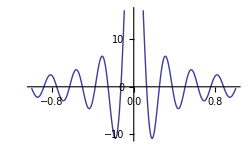

```mathematica
Plot[Sin[(q a n)/2]/Sin[(q a)/2],{q,-a,a},PlotRange->Automatic]
```

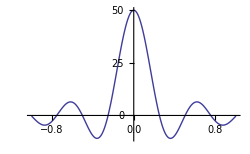

```mathematica
Plot[Sin[(q a n)/4]/Sin[(q a)/4],{q,-a,a},PlotRange->Automatic]
```

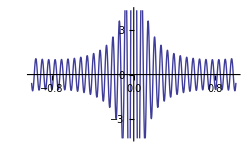

```mathematica
Plot[Sin[(q a n)/(.5)]/Sin[(q a)/(.5)],{q,-a,a},PlotRange->Automatic]
```

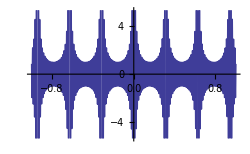

```mathematica
Plot[Sin[(q a n)/(.1)]/Sin[(q a)/(.1)],{q,-a,a},PlotRange->Automatic]
```

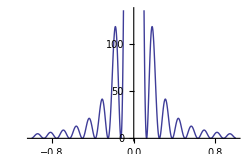

```mathematica
Plot[(Sin[(q a n)/2]/Sin[(q a)/2])^2,{q,-a,a},PlotRange->Automatic]
```

```mathematica
Plot3D[Exp[(-y q a)/2] Sinh[(q a n)/2]/Sinh[(q a)/2],{q,-1/n,1/n},{y,-5,5}]
```

-Graphics3D-

```mathematica
Clear[a,n]
```

```mathematica
Realizing the symmetry of each ordinate:
```

```mathematica
a∈Reals;
```

```mathematica
n∈Reals;
```

```mathematica
Exp[(-ⅈ q a)/2] Sinh[(q a n)/2]/Sinh[(q a)/2] Exp[(-ⅈ q b)/2] Sinh[(q b n)/2]/Sinh[(q b)/2] Exp[(-ⅈ q c)/2] Sinh[(q a c)/2]/Sinh[(q c)/2]
```

```mathematica
FullSimplify[Sqrt[Conjugate[Exp[(-ⅈ q a)/2] Sinh[(q a n)/2]/Sinh[(q a)/2] Exp[(-ⅈ q b)/2] Sinh[(q b n)/2]/Sinh[(q b)/2] Exp[(-ⅈ q c)/2] Sinh[(q a c)/2]/Sinh[(q c)/2]]Exp[(-ⅈ q a)/2] Sinh[(q a n)/2]/Sinh[(q a)/2] Exp[(-ⅈ q b)/2] Sinh[(q b n)/2]/Sinh[(q b)/2] Exp[(-ⅈ q c)/2] Sinh[(q a c)/2]/Sinh[(q c)/2]]]^2
```

ⅇ^(-ⅈ (a+b+c) q+ⅈ Re[(a+b+c) q]) Csch[(a q)/2] Csch[(b q)/2] Csch[(c q)/2] Csch[1/2 Conjugate[a] Conjugate[q]] Csch[1/2 Conjugate[b] Conjugate[q]] Csch[1/2 Conjugate[c] Conjugate[q]] Sinh[(a c q)/2] Sinh[(a n q)/2] Sinh[(b n q)/2] Sinh[1/2 Conjugate[a c q]] Sinh[1/2 Conjugate[a n q]] Sinh[1/2 Conjugate[b n q]]

```mathematica
The individual quantum numbers still cancel as in the 1D case and the result is the same.
```

```mathematica
Part D: The norm squared of Fourier Tansformed density function does this readily and obviously enough. This is the expectation value of the system.
```

```mathematica
Limit[N/(2*Pi),N->∞]
```

∞

```mathematica
Alternatively, we may plot the Fourier Transformed density function.  In real space, the delta function has issues at the value where it becomes infinite over an infintessimal ordinate (norm of the partition goes to zero)-which is typically at zero, for an unmodified delta function.  In the Fourier reciporical space, the delta function goes to infinity as F[q] goes to zero, since q goes to negative infinity.  This is the important condition since the meaning of ordinate and abscissa are reciporicated with respect to regular space.
```

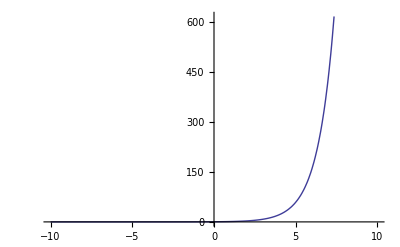

```mathematica
Plot[ⅇ^q/(√(2 π)),{q,-10,10}]
```